```mathematica
(*Домашна Работа №1 - Никола Тотев - Фн 62271 - Група 6*)

E^0.1
1.1051709180756477
E^0.2
1.2214027581601699
E^0.3
1.3498588075760032
```

```mathematica
l1[x_] = 1*(((x-0.1)(x-0.2)(x-0.3))/((0-0.1)(0-0.2)(0-0.3)));
l2[x_] = 1.10517 * (((x-0)(x-0.2)(x-0.3))/((0.1-0)(0.1-0.2)(0.1-0.3)));
l3[x_] = 1.2212*(((x-0)(x-0.1)(x-0.3))/((0.2-0)(0.2-0.1)(0.2-0.3)));
l4[x_] = 1.3498*(((x-0)(x-0.1)(x-0.2))/((0.3-0)(0.3-0.1)(0.3-0.2)));
p[x_] = l1[x]+l2[x]+l3[x]+l4[x];
```

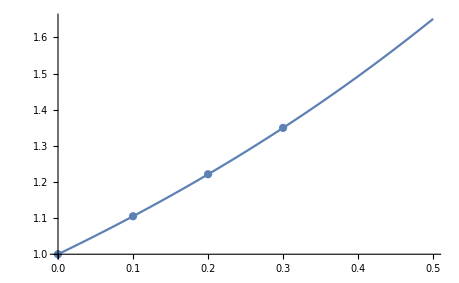
```mathematica
plot1 = Plot[p[x], {x, 0 , 0.5}];
plot2 = ListPlot[{{0, 1}, {0.1, 1.10517},{0.2, 1.2214},{0.3, 1.3498}}];
Show[{plot1, plot2}]
-Graphics-
```

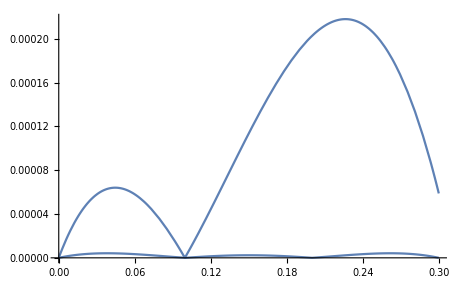
```mathematica
T[x_] = (x-0)(x-0.1)(x-0.2)(x-0.3); (*Омега от х*)
R[x_] = 1/24(T[x]); (*Оценка на грешката*)
A[x_] = E^x-p[x]; (*Самата грешка*)

plotA = Plot[Abs[A[x]], {x, 0, 0.3}];
plotR = Plot[Abs[R[x]],{x,0,0.3}];
Show[plotA, plotR, Plotrange->All]
-Graphics-
```

```mathematica
p[0.15]
1.161720625
```

```mathematica
E^0.15
1.161834242728283
```

```mathematica
E^0.15 - p[0.15] 
0.00011361772828299976
```